# Reviewing Probability

We will discuss the concept of probability and how it relates to the frequency of different outcomes in a repeatable measurement. Then we will show how probabilities in quantum theory help us calculate joint and marginal probabilities.

## Key Concepts

Random outcome

Probability distribution

Marginal probability

Joint probability

## Experiments and Randomness

You’re no doubt familiar with coin flips or dice rolls as ways to generate random outcomes. For our purposes, think of a random outcome as a definite result from a repeatable experiment. Randomness here means that several different outcomes are possible, and while we may know their probabilities, there is no way to determine which specific outcome will occur before running the experiment.

You can find much more information on probability and statistics in any of the following Wolfram U courses:

Introduction to Probability

Introduction to Statistics

Quantum theory provides a way to compute the probability distribution over possible measurement outcomes. You can think of a probability distribution as a rule that assigns a nonnegative probability to each possible outcome of an experiment, with all probabilities adding up to 1. In quantum circuits, this distribution is typically defined over the discrete set of possible bitstrings.

Let’s look at a couple examples of generating random outcomes to build intuition.

## Frequency vs probability

Suppose you want to choose a random whole number between 1 and 10. As with many concepts in probability and statistics, there is a built-in Wolfram Language function for this:

```mathematica
RandomInteger[{1,10}]
```

6

The above function returns a uniformly random integer from 1 to 10 (inclusive).

You can also simulate a sequence of random choices:

```mathematica
RandomInteger[{1,10},20]
```

{6,6,9,7,1,2,5,7,5,3,3,4,4,1,3,8,2,1,2,4}

The experiment to “choose a random whole number between 1 and 10” generally assumes that random means each number has an equal probability to be chosen. Let’s look at some specific data to see that your intuitions about equal probability for outcomes must be considered carefully. You can use SeedRandom to give simulated random results reproducibility:

```mathematica
SeedRandom[2134];
numberdata=RandomInteger[{1,10},20]
```

{5,5,7,6,5,2,6,2,9,9,5,2,10,7,10,8,9,3,2,5}

The following histogram shows some features of this outcome that may surprise you:

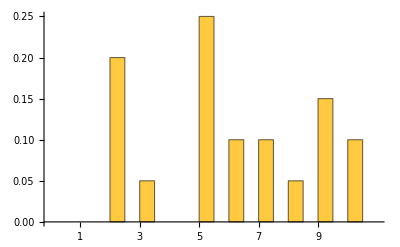

```mathematica
Histogram[numberdata,{.5},"Probability",Ticks->{Range[10],Automatic},PlotRange->{{0,11},All}]
```

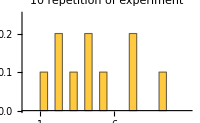
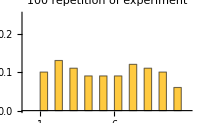
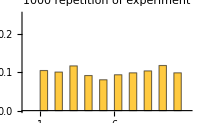
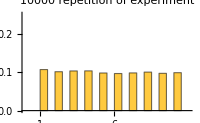
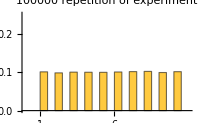

```mathematica
Row[Table[Histogram[RandomInteger[{1,10},j],{.5},"Probability",Ticks->{Range[10],Automatic},PlotRange->{{0,11},{0,.25}},PlotLabel->ToString[j]<>" repetition of experiment",ImageSize->200],{j,10^Range[5]}]]
```

As you can see, with more repetition of the same experiment, the observed frequency of outcomes gets closer to the true probability distribution. That said, any finite sample can show quirky deviations, which is why repeating an experiment many times is the best way to confirm that the expected distribution accurately describes it.

Now let’s consider the case where we assign a specific weight to each number: {1,1,2,3,4,4,3,2,1,1}.
We can compute the corresponding probabilities by normalizing the weights; that is:

```mathematica
probWeights=Normalize[{1,1,2,3,4,4,3,2,1,1},Total]
```

{1/22,1/22,1/11,3/22,2/11,2/11,3/22,1/11,1/22,1/22}

If we run the experiment many times, we expect the frequency of results to converge to the probabilities above. Now let’s generate different data samples of results for 10, 100, and 10,000 runs. As the number of realizations increases, the observed frequencies should get closer to the expected probabilities.

```mathematica
sequenceOfResults=Table[RandomChoice[{1,1,2,3,4,4,3,2,1,1}->Range[10],j],{j,{10,100,10000}}];
```

Calculate frequencies for each experiment:

```mathematica
freq=KeySort[Join[AssociationThread[Range[10]->0],Normalize[Counts[#],Total]]]&/@sequenceOfResults
```

{<|1→1/10,2→0,3→1/10,4→1/10,5→1/10,6→1/5,7→3/10,8→1/10,9→0,10→0|>,<|1→3/100,2→1/25,3→1/10,4→11/100,5→21/100,6→6/25,7→1/10,8→1/10,9→1/20,10→1/50|>,<|1→443/10000,2→231/5000,3→469/5000,4→33/250,5→1821/10000,6→229/1250,7→671/5000,8→953/10000,9→91/2000,10→217/5000|>}

Visualize the results:

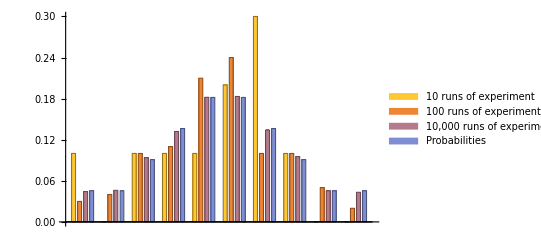

```mathematica
BarChart[Transpose@Append[Values/@freq,probWeights],ChartLegends->{"10 runs of experiment","100 runs of experiment","10,000 runs of experiment","Probabilities"}]
```

As expected, with more runs of the experiment, the observed frequencies get closer to the expected probabilities (law of large numbers).

Now let’s consider a case analogous to three different players rolling dice and collecting their joint outcomes. Of course, the quantum case can differ markedly from the classical one—classically, similar correlations might require prearranged strategies or communication. For the moment, however, we will set aside interpretation and focus only on the probabilities of the outcomes (i.e., the joint distribution and any marginals), leaving the discussion of correlations for later.

## Joint vs marginal probabilities

Consider a three-qubit system. Each qubit is measured in the computational basis, so any measurement result can be described by a three-bit string; overall 2^3 possible outcomes:

```mathematica
Tuples[{0,1},3]
```

{{0,0,0},{0,0,1},{0,1,0},{0,1,1},{1,0,0},{1,0,1},{1,1,0},{1,1,1}}

We will prepare the system in a special initial state. For now, we will skip the details of what this state is and focus only on the probability of outcomes. Later, we will elaborate on the details of this state and what it means.

```mathematica
state=QuantumState["RandomPure"[3]];
𝒟=QuantumMeasurementOperator[{{1},{2},{3}}][state]["MultivariateDistribution"];
```

Using quantum theory, we can calculate the joint probabilities of the measurement results, that is, the probabilities for all possible tuples of 0s and 1s listed above.

Visualize the contingency table of the distribution:

```mathematica
Information[𝒟,"ProbabilityTable"]
```

We can use the multivariate distribution and compute the probability of each outcome:

```mathematica
prob={#,PDF[𝒟,#]}&/@Tuples[{0,1},3];
TableForm[prob,TableDepth->2,TableHeadings->{None, {"Outcome","Probability"}}]
```

Outcome | Probability
{0,0,0} | 0.0528746
{0,0,1} | 0.214986
{0,1,0} | 0.112467
{0,1,1} | 0.259786
{1,0,0} | 0.024391
{1,0,1} | 0.207199
{1,1,0} | 0.0779609
{1,1,1} | 0.0503351

Since we have the multivariate distribution, we can compute the probability of any scenario by summing over the appropriate outcomes. Let’s consider a few cases.

Calculate the probability of getting 0 for qubit-1 and 1 for qubit-3 (and any result for qubit-2)

```mathematica
Probability[q1==0&&q3==1,{q1,q2,q3}\[Distributed]𝒟]
```

0.474772

Let’s calculate the above probability step-by-step:
- From the full list of outcome–probability pairs, select the outcomes whose first bit is 0 and last bit is 1 (i.e., {0,b,1} with be can be either 0 or 1, but we do not care).
- Extract the probabilities associated with those selected outcomes.
- Add those probabilities together.

```mathematica
Total@Select[prob,#[[1,1]]==0&&#[[1,3]]==1&][[All,-1]]
```

0.474772

Now suppose we do not care about qubit 3 and want to focus only on the statistics of qubits 1 and 2. To do this, we compute the marginal distribution by summing over the outcomes of qubit 3. (In the quantum formalism, this corresponds to taking the partial trace over qubit 3 to obtain the reduced state of qubits 1 and 2.)

To get the marginal distribution, the calculation as follows:
- first group outcomes based on the values of the first and second elements (we are only interested in the marginal distribution qubit 1 and 2)
- for each group, add up the values of probabilities

```mathematica
GroupBy[prob,(#[[1]][[;;2]]&)->Last,Total]
```

<|{0,0}→0.267861,{0,1}→0.372253,{1,0}→0.23159,{1,1}→0.128296|>

The same process can be done more cleanly using built-in Wolfram Language functionality. This makes it much easier to compute other probabilities as well (you’ll see this shortly).

Calculate  the marginal distribution

```mathematica
𝒟12=MarginalDistribution[𝒟,{1,2}]
```

CategoricalDistribution[…]

Visualize the contingency table of the marginal distribution:

```mathematica
Information[𝒟12,"ProbabilityTable"]
```

Calculate the probability of getting 0 for qubit-1 from the marginal probability distribution:

```mathematica
Probability[q1==0,{q1,q2}\[Distributed]𝒟12]
```

0.640114

Calculate the probability of getting 0 for qubit-1 from the overall probability distribution:

```mathematica
Probability[q1==0,{q1,q2,q3}\[Distributed]𝒟]
```

0.640114

Of course, the rules of quantum theory provide a recipe for obtaining the quantum state of qubits 1 and 2 by averaging over all contributions from qubit 3. This is done by tracing over the degrees of freedom of qubit 3, which yields the reduced state for qubits 1 and 2.

Trace out the qubit-3 (which is the 3rd subsystem) from the overall state:

```mathematica
QuantumPartialTrace[state,{3}]
```

QuantumState[…]

And this reduced state yields the same marginal probabilities as before:

```mathematica
QuantumPartialTrace[state,{3}]["Probabilities"]
```

<|00→0.267861,01→0.372253,10→0.23159,11→0.128296|>

```mathematica
Information[𝒟12,"Probabilities"]
```

<|{0,0}→0.267861,{0,1}→0.372253,{1,0}→0.23159,{1,1}→0.128296|>

In future chapters, we will discuss in details the idea of tracing out a subsystem and how to describe the state of composite systems in quantum theory.

## Initialization

Install Wolfram quantum framework

```mathematica
PacletInstall["https://www.wolfr.am/DevWQCF",ForceVersionInstall->True]
<<Wolfram`QuantumFramework`
```

PacletObject[…]